```mathematica
SummaryPrintGood5[k_]:=With[
{g=MobiusGraphDoubleGood[K5Key,k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
Graph[g,ImageSize->650]
}],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[StandardForm[allGraphs5[k,"colofour"]],Darker[Blue],12],
Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[m<->Style[ChromaticPolynomial[gr,m],Blue],{m,1,5}], " * "],
Framed[Style[StandardForm[((allGraphs5[k,"colofour"])/.repBase5Bare)],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

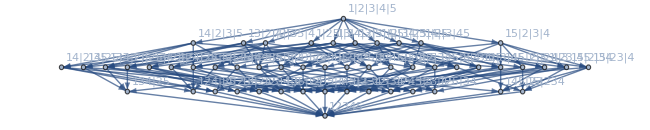
{-Graphics-36085-Graphics--6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5v13x2x4x5
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-,-Graphics-29605-Graphics--6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n135x24+n13x245-n13x24x5+n15x234-n15x24x3+2 n1x2345-n1x234x5-n1x245x3-n1x24x35+n1x24x3x5v1x24x3x5
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-,-Graphics-29527-Graphics--6 n12345+2 n1235x4+2 n124x35+n12x345-n12x35x4+2 n1345x2+n135x24-n135x2x4+n14x235-n14x2x35+2 n1x2345-n1x235x4-n1x24x35-n1x2x345+n1x2x35x4v1x2x35x4
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-,-Graphics-31711-Graphics--6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n1345x2+n134x25-n134x2x5+n145x23-n145x2x3+2 n14x235-n14x23x5-n14x25x3-n14x2x35+n14x2x3x5v14x2x3x5
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-,-Graphics-29551-Graphics--6 n12345+2 n1235x4+2 n1245x3+n125x34-n125x3x4+2 n134x25+n13x245-n13x25x4+n14x235-n14x25x3+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4v1x25x3x4
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-}

```mathematica
Table[SummaryPrintGood5[k],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

```mathematica
Table[SummaryPrintGood5[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{-Graphics-36166-Graphics-2 n12345-n1234x5-n135x24-n13x245+n13x24x5v13x24x5
x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 1<->02<->03<->64<->245<->60
-Graphics-,-Graphics-31738-Graphics-2 n12345-n1245x3-n134x25-n14x235+n14x25x3v14x25x3
x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 1<->02<->03<->64<->245<->60
-Graphics-,-Graphics-29608-Graphics-2 n12345-n124x35-n135x24-n1x2345+n1x24x35v1x24x35
x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 1<->02<->03<->64<->245<->60
-Graphics-,-Graphics-36112-Graphics-2 n12345-n1235x4-n134x25-n13x245+n13x25x4v13x25x4
x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 1<->02<->03<->64<->245<->60
-Graphics-,-Graphics-31714-Graphics-2 n12345-n124x35-n1345x2-n14x235+n14x2x35v14x2x35
x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 1<->02<->03<->64<->245<->60
-Graphics-}

```mathematica
SummaryPrintGood5[quad1Key]
```

-Graphics-36085-Graphics--6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5v13x2x4x5
x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
 *  * 1<->02<->03<->04<->245<->120
-Graphics-

```mathematica
SummaryPrintGood5[lambdaKey]
```

-Graphics-20665-Graphics-4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5
x^5-5 x^4+10 x^3-10 x^2+4 x
(x-2) (x-1) x (x^2-2 x+2)
 *  * 1<->02<->03<->304<->2405<->1020
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Binomial[5,3]
```

10

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3]&]
```

{29537,29560,29608,29633,29768,29797,29857,30262,30334,30496,31714,31738,31954,32441,36086,36112,36166,36817,38281,49208,49210,49216,49963,51475,56011}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[{k,allGraphs5[k,"compwhy"]},ColourForKey[allGraphs5,k]]],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==6]&]}]
```

{-Graphics-{29525,No IH},-Graphics-{29527,No IH},-Graphics-{29533,No IH},-Graphics-{29551,No IH},-Graphics-{29605,No IH},-Graphics-{29767,No IH},-Graphics-{30253,No IH},-Graphics-{31711,No IH},-Graphics-{36085,No IH},-Graphics-{49207,No IH}}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[{k,allGraphs5[k,"compwhy"]},ColourForKey[allGraphs5,k]]],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==3&&EdgeCount[g]==3]&]}]
```

{-Graphics-{29537,This is a planar contraction},-Graphics-{29560,No IH},-Graphics-{29608,No IH},-Graphics-{29633,No IH},-Graphics-{29768,This is a planar contraction},-Graphics-{29797,No IH},-Graphics-{29857,This is a planar contraction},-Graphics-{30262,This is a planar contraction},-Graphics-{30334,No IH},-Graphics-{30496,This is a planar contraction},-Graphics-{31714,No IH},-Graphics-{31738,No IH},-Graphics-{31954,No IH},-Graphics-{32441,This is a planar contraction},-Graphics-{36086,No IH},-Graphics-{36112,No IH},-Graphics-{36166,No IH},-Graphics-{36817,No IH},-Graphics-{38281,No IH},-Graphics-{49208,This is a planar contraction},-Graphics-{49210,No IH},-Graphics-{49216,This is a planar contraction},-Graphics-{49963,This is a planar contraction},-Graphics-{51475,No IH},-Graphics-{56011,This is a planar contraction}}

```mathematica
StirlingS2[5,3]
```

25